```mathematica
SetDirectory[NotebookDirectory[]];
AppendTo[$Path,NotebookDirectory[]];
Needs["PenroseTilingFunctions`"]
```

```mathematica
checkers=Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
grid={EdgeForm[{Thin}],FaceForm[Transparent],#}&/@checkers;
blacks=Take[checkers,{1,-1,2}];
whites={White,#}&/@Drop[checkers,{1,-1,2}];
```

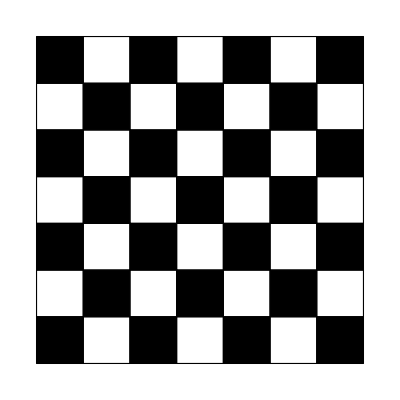

```mathematica
Graphics@{grid,blacks}
```

```mathematica
Export["Checkerboard.png",Graphics@{grid,blacks}]
```

Checkerboard.png

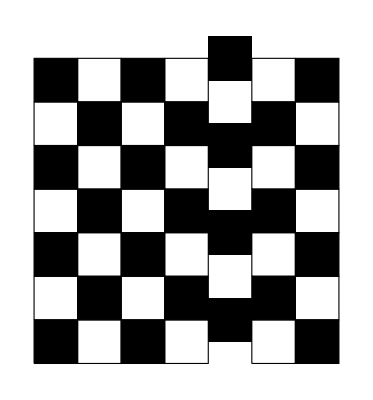

CheckerboardAperiodic.png

```mathematica
newgrid=Complement[grid,Cases[grid,{EdgeForm[{Thickness[Tiny]}],FaceForm[-Graphics-],Translate[Rectangle[{0,0}],{4,_}]}]];
Translate[#,{0,0.5}]&/@Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]];
Complement[blacks,Cases[blacks,Translate[Rectangle[{0,0}],{4,_}]]];
Graphics[{newgrid,%%,%}]
Export["CheckerboardAperiodic.png",%]
```

```mathematica
Flatten[Table[Translate[Rectangle[],{i,j}],{i,0,6},{j,0,6}],1];
newblacks=Take[%,{1,-1,3}];
```

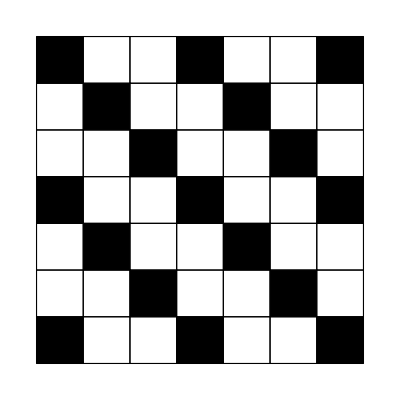

CheckerboardOther.png

```mathematica
Graphics@{grid,newblacks}
Export["CheckerboardOther.png",%]
```

```mathematica
circles=Flatten[Table[Translate[Disk[],{i,j}],{i,0,7,2},{j,0,7,2}],1];
```

```mathematica
Rotate[Graphics[{FaceForm[Black],#}&/@circles],Pi/4];
Graphics[Rotate[circles,Pi/4]]
Table[Graphics[Translate[Rotate[circles,Pi/4],{0,i*2Sqrt[2]}]],{i,-2,1}];
Show[{%,%%},PlotRange->{{-2.3,8.3},{-3.75,6.85}}]
Export["CheckerboardCircles.png",%]
```

-Graphics-

-Graphics-

CheckerboardCircles.png

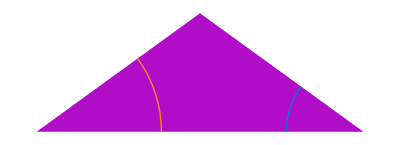

RobinsonFat.png

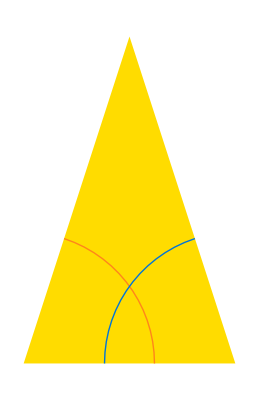

RobinsonSkinny.png

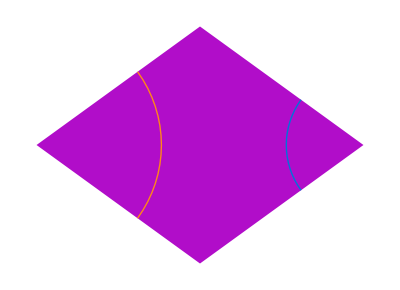

RhombFat.png

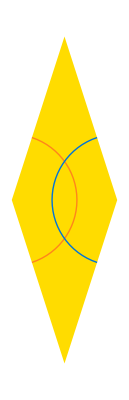

RhombSkinny.png

```mathematica
Show[See@{unitfat},Graphics[MakeCurveRules/@Inflate[{unitfat},0]]]
Export["RobinsonFat.png",%,Background->None,ImageResolution->200]
Show[See@{unitskinny},Graphics[MakeCurveRules/@Inflate[{unitskinny},0]]]
Export["RobinsonSkinny.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitfat},Graphics[MakeCurveRules/@AddConj@Inflate[{unitfat},0]]]
Export["RhombFat.png",%,Background->None,ImageResolution->200]
Show[See@AddConj@{unitskinny},Graphics[MakeCurveRules/@AddConj@Inflate[{unitskinny},0]]]
Export["RhombSkinny.png",%,Background->None,ImageResolution->200]
```

```mathematica
rhombfatunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitfat},Pi/5];
rhombskinnyunit=Rotate[Polygon/@Coor/@First/@Rhomb/@{unitskinny},2Pi/5];

rhombfatgrid=Flatten[Table[Translate[rhombfatunit,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];
rhombskinnygrid=Translate[Flatten[Table[Translate[rhombskinnyunit,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

fatrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitfat},0],Pi/5];
fatrulesgrid=Flatten[Table[Translate[fatrules,{i,j}],{i,0,6},{j,0,6,2*0.951}],1];

skinnyrules=Rotate[MakeCurveRules/@AddConj@Inflate[{unitskinny},0],2Pi/5];
skinnyrulesgrid=Translate[Flatten[Table[Translate[skinnyrules,{i,j}],{i,0,6,ϕ},{j,0.951,6,2*0.951}],1],{0.8,0}];

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodic.png",%,Background->None,ImageResolution->200]

Show[Graphics[{FaceForm[None],EdgeForm[Black],rhombfatgrid}],
Graphics[{FaceForm[None],EdgeForm[Black],rhombskinnygrid}],Graphics[fatrulesgrid],Graphics[skinnyrulesgrid],PlotRange->{{-1,7.3},{-0.6,6.5}}]
Export["RhombPeriodicRules.png",%,Background->None,ImageResolution->200]
```

-Graphics-

RhombPeriodic.png

-Graphics-

RhombPeriodicRules.png

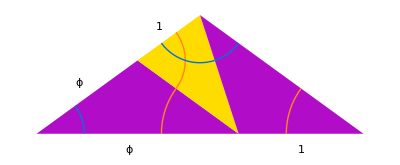

RobFatSub.png

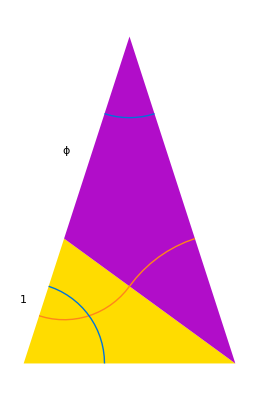

RobSkinnySub.png

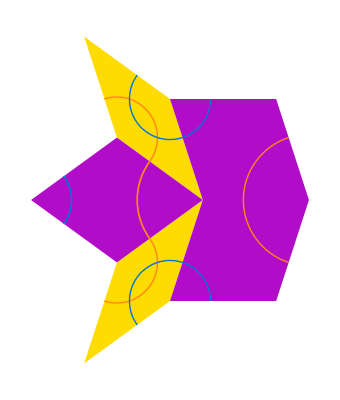

RhombFatSub.png

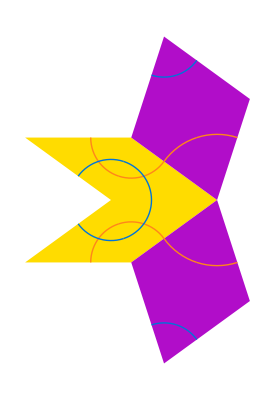

RhombSkinnySub.png

RobFatSub.png

-Graphics-

RobSkinnySub.png

-Graphics-

RhombFatSub.png

-Graphics-

RhombSkinnySub.png

```mathematica
Show[See@Inflate[{unitfat},1],Graphics[MakeCurveRules/@Inflate[{unitfat},1]],Graphics[Text[Style["ϕ",Large],{-0.6,0.25}]],Graphics[Text[Style["1",Large],{-0.2,0.53}]],Graphics[Text[Style["ϕ",Large],{-0.35,-0.08}]],Graphics[Text[Style["1",Large],{0.5,-0.08}]]]
Export["RobFatSub.png",%,Background->None,ImageResolution->200]
Show[See@Inflate[{unitskinny},1],Graphics[MakeCurveRules/@Inflate[{unitskinny},1]],Graphics[Text[Style["ϕ",Large],{-0.3,1}]],Graphics[Text[Style["1",Large],{-0.5,0.3}]]]
Export["RobSkinnySub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitfat},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitfat},1]]]
Export["RhombFatSub.png",%,Background->None,ImageResolution->200]
Show[See@FullInflate[{unitskinny},1],Graphics[MakeCurveRules/@AddConj@AddRhombTris@Inflate[{unitskinny},1]]]
Export["RhombSkinnySub.png",%,Background->None,ImageResolution->200]
```